Quantum splitting of electron peaks in ultra-strong fields

Zhang et al , Matter Radiat. Extremes 8, 054003 (2023)
Notebook: Óscar Amaro, September 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Figure 1

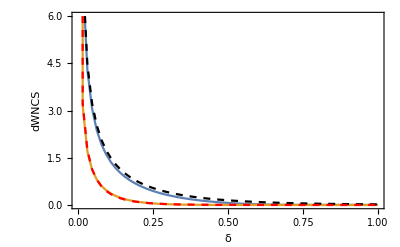

```mathematica
Clear[δ,χ,dWNCS,dWQSR,y,m,α,fin,γ]
m=p0=γ=1;
α=1/137;
(* NCS *)
dWNCS[χ_,δ_]:=α/(π Sqrt[3])m^2/p0((1-δ+1/(1-δ))BesselK[2/3,(2δ)/(3χ(1-δ))]-NIntegrate[BesselK[1/3,y],{y,(2δ)/(3χ(1-δ)),∞}])
A=300;
fin[χ_,δ_]:=0.5α m^2/p0 (χ/δ)^(2/3)Exp[-δ/χ];
Plot[{A dWNCS[0.3,δ],A dWNCS[0.1,δ],A fin[0.3,δ],A fin[0.1,δ]},{δ,0,1},PlotPoints->2,Frame->True,FrameLabel->{"δ","dWNCS"},PlotRange->{0,6},PlotStyle->{Default,Default,{Dashed,Black},{Red,Dashed}}]
```

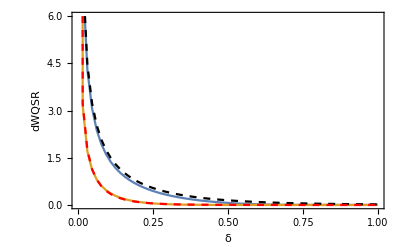

```mathematica
(* QSR *)

dWQSR[χ_,δ_]:=(Sqrt[3] α)/(2π)(m χ)/γ(1-δ)/δ((2δ)/(3χ(1-δ))NIntegrate[BesselK[5/3,x],{x,(2δ)/(3χ(1-δ)),∞}]+((2δ)/(3χ(1-δ)))^3(3χ/2)^2(1-δ)BesselK[2/3,(2δ)/(3χ(1-δ))])
A=300;
fin[χ_,δ_]:=0.5α m^2/p0 (χ/δ)^(2/3)Exp[-δ/χ];
Plot[{A dWQSR[0.3,δ],A dWQSR[0.1,δ],A fin[0.3,δ],A fin[0.1,δ]},{δ,0,1},PlotPoints->2,Frame->True,FrameLabel->{"δ","dWQSR"},PlotRange->{0,6},PlotStyle->{Default,Default,{Dashed,Black},{Red,Dashed}}]
```

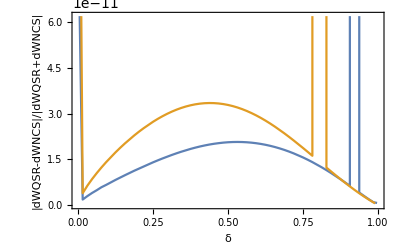

```mathematica
(* difference between NCS and QSR *)
Plot[{Abs[(dWNCS[0.3,δ]- dWQSR[0.3,δ])/(dWNCS[0.3,δ]+ dWQSR[0.3,δ])],Abs[(dWNCS[0.1,δ]- dWQSR[0.1,δ])/(dWNCS[0.1,δ]+ dWQSR[0.1,δ])]},{δ,0,1},PlotPoints->2,Frame->True,FrameLabel->{"δ","|dWQSR-dWNCS|/|dWQSR+dWNCS|"}]
```

## Equation 13

```mathematica
Clear[R,χ,δ,f1,f2]
R[δ_]:=χ^(-1/3) δ^(-2/3) Exp[-δ/χ]/Gamma[1/3]
f1=R[1-δ] (* written with argument δ *)
f2=Integrate[f1 R[δ-η],{δ,η,1}]//Normal (* written with argument η *)
f3=Integrate[f2 R[η-δ],{η,δ,1}]//Normal (* written with argument δ *)
```

ⅇ^((-1+δ)/χ)/((1-δ)^(2/3) χ^(1/3) Gamma[1/3])

(ⅇ^((-1+η)/χ) Gamma[1/6])/(2^(2/3) √π (1-η)^(1/3) χ^(2/3) Gamma[1/3])

ⅇ^((-1+δ)/χ)/χ

```mathematica
(* check for i=2,3 *)
fi[i_,χ_,δ_]:=χ^(-i/3)/Gamma[i/3] (1-δ)^(i/3-1) Exp[-(1-δ)/χ]
f2-fi[2,χ,η]//FullSimplify
f3-fi[3,χ,δ]//FullSimplify
```

0

0

## Root of dFdη

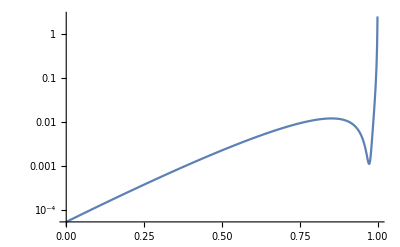

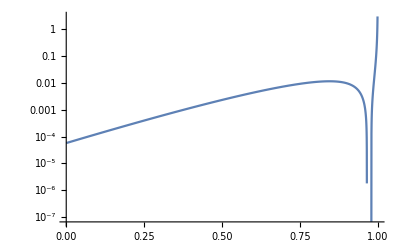

```mathematica
(* Showing graphically that the threshold is r~5.35 *)
Clear[dFdη,χ,r,η,ξ]
χ=0.1;

r=5.3;
dFdη=-χ Exp[-r]Exp[-ξ]Sum[(r^i ((i/3-1)ξ^(i/3-2)-ξ^(i/3-1)))/(i! Gamma[i/3]),{i,1,20}]/.{ξ->(1-η)/χ}//N;
LogPlot[dFdη,{η,0,1}]

r=5.4;
dFdη=-χ Exp[-r]Exp[-ξ]Sum[(r^i ((i/3-1)ξ^(i/3-2)-ξ^(i/3-1)))/(i! Gamma[i/3]),{i,1,20}]/.{ξ->(1-η)/χ}//N;
LogPlot[dFdη,{η,0,1}]
```

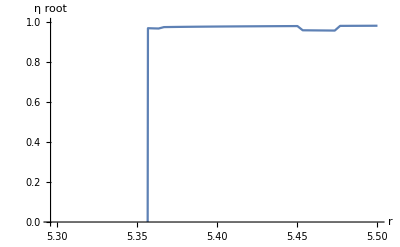

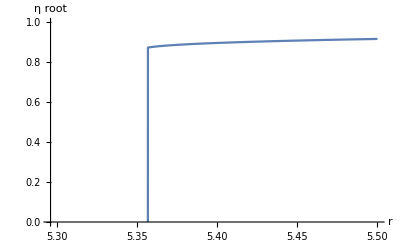

```mathematica
(* more precise proof that the threshold is r~5.35 *)
Clear[dFdη,χ,r,η,ξ]
χ=0.1;
dFdη[r_]:=-χ Exp[-r]Exp[-ξ]Sum[(r^i ((i/3-1)ξ^(i/3-2)-ξ^(i/3-1)))/(i! Gamma[i/3]),{i,1,40}]/.{ξ->(1-η)/χ}//N;
ListPlot[Table[{r,FindRoot[{dFdη[r]==0},{η,0.9}][[1,2]]},{r,5.3,5.5,0.01/3}],Joined->True,PlotRange->{0,1},AxesLabel->{"r","η root"}]//Quiet

Clear[dFdη,χ,r,η,ξ]
χ=0.5;
dFdη[r_]:=-χ Exp[-r]Exp[-ξ]Sum[(r^i ((i/3-1)ξ^(i/3-2)-ξ^(i/3-1)))/(i! Gamma[i/3]),{i,1,40}]/.{ξ->(1-η)/χ}//N;
ListPlot[Table[{r,FindRoot[{dFdη[r]==0},{η,0.9}][[1,2]]},{r,5.3,5.5,0.01/3}],Joined->True,PlotRange->{0,1},AxesLabel->{"r","η root"}]//Quiet
```